```mathematica
<<ChemTools`
<<ChemTools`Data`
<<ChemTools`Utilities`
```

```mathematica
Get["~/Documents/UW/Research/H5+/Common/H5Core.m"];
Get["~/Documents/UW/Research/H5+/Common/SpectrumScript.m"];
```

#### Extrapolate Potential

```mathematica
getFit[slice_]:=
Module[
{
fit1=
LinearModelFit[slice, r^Range[6], r]
},
fit1
];
extrapolatePotentialSlice[shareProtPot_, potReg_]:=
Module[
{
rawGrid=
SortBy[#, #[[2]]&]&/@
SortBy[GatherBy[DeleteDuplicatesBy[shareProtPot, #[[;;2]]&], First], #[[1, 1]]&],
targetRange=potReg,
currRange,
rangeDiff,
meshSpacing,
extraPoints,
modelFit
},
Fold[
With[{n=Mod[#2+1, 2, 1]},
Transpose@
Table[
currRange=MinMax[slice[[All, n]]];
rangeDiff=targetRange-currRange;
meshSpacing=slice[[2, n]]-slice[[1, n]];
extraPoints=
Map[
Sort,
currRange+
meshSpacing*
Sign[rangeDiff]*Range[Floor[Abs[rangeDiff/meshSpacing]]]
];
modelFit=
getFit[slice[[All, {n, 3}]]];
Join[
If[Length@extraPoints[[1]]>0,
Join[
ConstantArray[slice[[1, #2]],{ Length@extraPoints[[1]],  1}],
Transpose@{
extraPoints[[1]],
modelFit["Function"]/@extraPoints[[1]]
},
2
],
Sequence@@{}
],
slice,
If[Length@extraPoints[[2]]>0,
Join[
ConstantArray[slice[[1, #2]],{ Length@extraPoints[[2]],  1}],
Transpose@{
extraPoints[[2]],
modelFit["Function"]/@extraPoints[[2]]
},
2
],
Sequence@@{}
]
],
{slice, #}
]
]&,
rawGrid,
Range[1]
]
];
extrapolatePotential[pot_]:=
Module[
{
potChunks,
saExtrapPot,
saExtrapJoins,
r1r2ExtrapPot,
r1r2ExtrapJoins,
fullPot
},
potChunks=
GroupBy[pot, (#[[{1, 2}]]&)->(#[[{3, 4, 5}]]&)];
saExtrapPot=
extrapolatePotentialSlice[#, $H5PotentialRegion[[3]]]&/@potChunks;
saExtrapJoins=
Flatten[
KeyValueMap[
Join[
ConstantArray[#,Times@@Dimensions[#2][[;;-2]] ],
Flatten[#2, 1],
2
]&,
saExtrapPot
],
1
];
potChunks=GroupBy[saExtrapJoins, (#[[{3, 4}]]&)->(#[[{1, 2, 5}]]&)];
r1r2ExtrapPot=extrapolatePotentialSlice[#, $H5PotentialRegion[[1]]]&/@potChunks;
fullPot=
Flatten[
KeyValueMap[
Join[
Flatten[#2, 1][[All, ;;2]],
ConstantArray[#,Times@@Dimensions[#2][[;;-2]]],
Flatten[#2, 1][[All, {3}]],
2
]&,
r1r2ExtrapPot
],
1
]
]
```

#### Basic Scan

```mathematica
scanLog="~/Documents/UW/Research/H5+/scans/outer_H2_scan.log";
scanImp=Import[scanLog, {"GaussianLog", "ScanQuantityArray"}];
```

##### Potential

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/potential.mx", 
scanImp[[2]]
]
```

Part::partw: Part 2 of Missing[NotFound] does not exist.

~/Documents/UW/Research/H5+/inputs/potential.mx

```mathematica
testPoot=
With[{poot1=QuantityMagnitude@scanImp[[2]]},
QuantityArray[
Sort@extrapolatePotential[
poot1-ConstantArray[{0., 0., 0., 0., Min@poot1}, Length@poot1]
], 
QuantityUnit@scanImp[[2, 1]]
]
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/potential.mx", 
(*scanImp[[2]]*)testPoot
]
```

~/Documents/UW/Research/H5+/inputs/potential.mx

##### Dipole

```mathematica
getRecenteredDipoleMoments[dCoords_]:=
Module[
{weirdRCoeff, dipVecs, qa},
qa=Developer`ToPackedArray@dCoords;
weirdRCoeff=
4.8032047128700560408`7.948154179081327
(*QuantityMagnitude[
UnitConvert["ElementaryCharge"*"BohrRadius", "Debyes"]/UnitConvert["BohrRadius", "Angstroms"]
]*);
dipVecs=
qa[[ All, {5, 6, 7}]]-
Thread[
{
weirdRCoeff*(3*qa[[All, 3]]+2*qa[[All, 4]])/5
(*(qa[[All, 3]]-qa[[All, 4]])*weirdRCoeff/2*),
0.,
weirdRCoeff*qa[[All, 1]]
}
];
Join[
Developer`ToPackedArray@qa[[All, {1, 2, 3, 4}]],
Developer`ToPackedArray@dipVecs,
2
]
];
```

```mathematica
scanDipCoords=
QuantityArray[
getRecenteredDipoleMoments@
Join[
QuantityMagnitude@scanImp[[2, All, ;;4]],
QuantityMagnitude@scanDip,
2
],
Join[
QuantityUnit@scanImp[[2, 1, ;;4]],
QuantityUnit@scanDip[[1]]
]
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/outer_H2_dipole.mx", 
scanDipCoords
]
```

~/Documents/UW/Research/H5+/inputs/outer_H2_dipole.mx

#### Parallel Scan

##### Inputs

```mathematica
scanLogP="/Users/Mark/Documents/UW/Research/H5+/scans/outer_H2_scan_new_parallel.log";
scanImpP=Import[scanLogP, {"GaussianLog", "ScanQuantityArray"}];
scanDipP=Import[scanLogP, {"GaussianLog", "DipoleQuantityArray"}];
```

##### Potential

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/potential_parallel.mx", 
scanImpP[[2]]
]
```

~/Documents/UW/Research/H5+/inputs/potential_parallel.mx

##### Dipole

```mathematica
getRecenteredDipoleMoments[dCoords_]:=
Module[
{weirdRCoeff, dipVecs, qa},
qa=Developer`ToPackedArray@dCoords;
weirdRCoeff=
4.8032047128700560408`7.948154179081327
(*QuantityMagnitude[
UnitConvert["ElementaryCharge"*"BohrRadius", "Debyes"]/UnitConvert["BohrRadius", "Angstroms"]
]*);
dipVecs=
qa[[ All, {5, 6, 7}]]-
Thread[
{
weirdRCoeff*(3*qa[[All, 3]]+2*qa[[All, 4]])/5
(*(qa[[All, 3]]-qa[[All, 4]])*weirdRCoeff/2*),
0.,
2*weirdRCoeff*qa[[All, 1]]
}
];
Join[
Developer`ToPackedArray@qa[[All, {1, 2, 3, 4}]],
Developer`ToPackedArray@dipVecs,
2
]
];
```

```mathematica
scanDipCoordsP=
QuantityArray[
getRecenteredDipoleMoments@
Join[
QuantityMagnitude@scanImpP[[2, All, ;;4]],
QuantityMagnitude@scanDipP,
2
],
Join[
QuantityUnit@scanImpP[[2, 1, ;;4]],
QuantityUnit@scanDipP[[1]]
]
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/outer_H2_dipole_parallel.mx", 
scanDipCoordsP
]
```

~/Documents/UW/Research/H5+/inputs/outer_H2_dipole_parallel.mx

#### New Stuff

```mathematica
scanLog="~/Documents/UW/Research/H5+/scans/outer_H2_scan_new.log";
```

```mathematica
scanImp=Developer`ToPackedArray/@
Import[scanLog, "GaussianLog", 
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
scanImp["MP2Energies"][[1]]
```

```mathematica
wnConv=QuantityMagnitude@ChemUnitConvert["Hartrees", "Wavenumbers"];
```

```mathematica
coordinateArray=
Pick[#, UnitStep[4.3-#[[All, 3]]], 1]&@
Join[
scanImp[["ZMatrixCoordinateVectors", All, {4,-3,  7,-9}]],
ArrayReshape[wnConv*#, {Length[#], 1}]&@scanImp["MP2Energies"],
scanImp["DipoleMoments"],
2
];
```

```mathematica
potArray=
QuantityArray[coordinateArray[[All, ;;5]], 
Append[ConstantArray["Angstroms", 4], "Wavenumbers"]
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/potential.mx", 
potArray
]
```

~/Documents/UW/Research/H5+/inputs/potential.mx

```mathematica
dipArrayBasic=
QuantityArray[coordinateArray[[All, ;;5]], 
Append[ConstantArray["Angstroms", 4], "Wavenumbers"]
];
```

##### Inputs

```mathematica
scanLogP="/Users/Mark/Documents/UW/Research/H5+/scans/outer_H2_scan_new_parallel.log";
scanImpP=Import[scanLogP, {"GaussianLog", "ScanQuantityArray"}];
scanDipP=Import[scanLogP, {"GaussianLog", "DipoleQuantityArray"}];
```

##### Potential

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/potential_parallel.mx", 
scanImpP[[2]]
]
```

~/Documents/UW/Research/H5+/inputs/potential_parallel.mx

##### Dipole

```mathematica
getRecenteredDipoleMoments[dCoords_]:=
Module[
{weirdRCoeff, dipVecs, qa},
qa=Developer`ToPackedArray@dCoords;
weirdRCoeff=
4.8032047128700560408`7.948154179081327
(*QuantityMagnitude[
UnitConvert["ElementaryCharge"*"BohrRadius", "Debyes"]/UnitConvert["BohrRadius", "Angstroms"]
]*);
dipVecs=
qa[[ All, {5, 6, 7}]]-
Thread[
{
weirdRCoeff*(3*qa[[All, 3]]+2*qa[[All, 4]])/5
(*(qa[[All, 3]]-qa[[All, 4]])*weirdRCoeff/2*),
0.,
2*weirdRCoeff*qa[[All, 1]]
}
];
Join[
Developer`ToPackedArray@qa[[All, {1, 2, 3, 4}]],
Developer`ToPackedArray@dipVecs,
2
]
];
```

```mathematica
scanDipCoordsP=
QuantityArray[
getRecenteredDipoleMoments@
Join[
QuantityMagnitude@scanImpP[[2, All, ;;4]],
QuantityMagnitude@scanDipP,
2
],
Join[
QuantityUnit@scanImpP[[2, 1, ;;4]],
QuantityUnit@scanDipP[[1]]
]
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/outer_H2_dipole_parallel.mx", 
scanDipCoordsP
]
```

~/Documents/UW/Research/H5+/inputs/outer_H2_dipole_parallel.mx

#### New Stuff Parallel

```mathematica
scanLogP="~/Documents/UW/Research/H5+/scans/outer_H2_scan_new_parallel.log";
```

```mathematica
scanImpP=Developer`ToPackedArray/@
Import[scanLogP, "GaussianLog", 
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
wnConv=QuantityMagnitude@ChemUnitConvert["Hartrees", "Wavenumbers"];
```

```mathematica
coordinateArrayP=
Pick[#, UnitStep[4.3-#[[All, 3]]], 1]&@
Join[
scanImpP[["ZMatrixCoordinateVectors", All, {4,-3,  7,-9}]],
ArrayReshape[wnConv*#, {Length[#], 1}]&@scanImpP["MP2Energies"],
scanImpP["DipoleMoments"],
2
];
```

```mathematica
potArrayP=
QuantityArray[coordinateArrayP[[All, ;;5]], 
Append[ConstantArray["Angstroms", 4], "Wavenumbers"]
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/inputs/potential_parallel.mx", 
potArrayP
]
```

~/Documents/UW/Research/H5+/inputs/potential_parallel.mx

### Old Useless Shit

#### Basic Scan Odl

```mathematica
scanLog="~/Documents/UW/Research/H5+/scans/outer_H2_scan.log";
scanImp=Import[scanLog, {"GaussianLog", "ScanQuantityArray"}]
```

```mathematica
rawArr=
QuantityArray[
QuantityMagnitude@Values@scanImp,
{"Angstroms","Angstroms", "Angstroms","Angstroms", "Hartrees"}
];
```

```mathematica
arr=scanImp;
```

```mathematica
UnitConvert[
rawArr,
{"Angstroms","Angstroms", "Angstroms","Angstroms","Wavenumbers"*("SpeedOfLight""PlanckConstant")}
];
```

```mathematica
subArrs=GroupBy[Normal@arr, Function@#[[{3, 4}]]->Function@#[[{1, 2, 5}]], QuantityArray];
```

```mathematica
subArrDiff[n_, m_]:=
QuantityArray@
MapThread[Append,
{
Normal@subArrs[[n, All, ;;2]], Normal[subArrs[[n, All, 3]]-subArrs[[m, All, 3]]]
}
];
```

```mathematica
Iconize[
arrMinMax=
Flatten@Table[
If[i<=j, Nothing, subArrDiff[j, i][[All, 3]]]//MinMax, 
{i, 1, Length@subArrs, 1},
{j, 1, Length@subArrs, 1}
]//MinMax,
"MinMax"
]
```

```mathematica
Manipulate[
ListDensityPlot[
QuantityMagnitude[If[i<j,subArrDiff[i, j],subArrDiff[j, i]]],
PlotRange->
{
Automatic,
Automatic,
QuantityMagnitude[]
},
PlotLabel->
TemplateApply[
"V(r_1, r_2;``, ``)-V(r_1, r_2;``, ``)",
QuantityMagnitude@Flatten@Keys[subArrs][[{i, j}]]
]
],
{{i, 1}, 1, Length@subArrs, 1},
{{j, 2}, 1, Length@subArrs, 1}
]
```

```mathematica
holyShit=Interpolation[QuantityMagnitude@arr]
```

InterpolatingFunction[…]

```mathematica
holyShit[[1]]
```

{{0.25,2.25},{0.25,2.25},{1.5107,3.5107},{1.5107,3.5107}}

```mathematica
Manipulate[
Plot3D[holyShit[r[[1]], r[[2]],R1, R2 ], 
{R1, 1.5107,3.5107}, {R2, 1.5107,3.5107},
PlotRange->
{
Automatic,
Automatic,
MinMax@QuantityMagnitude@arr[[All, -1]]
}],
{{r, {1, 1}}, {.25,.25}, {2.25,2.25}}
]
```

#### High Res At Eq

```mathematica
scanLogHR="~/Documents/UW/Research/H5+/outer_H2_scan_high_res.log";
rawArrHR=
QuantityArray[
QuantityMagnitude@Values@Import[scanLogHR, "GaussianScan"],
{"Angstroms", "Angstroms", "Hartrees"}
];
arrHR=
UnitConvert[
rawArrHR,
{"Angstroms","Angstroms","Wavenumbers"*("SpeedOfLight""PlanckConstant")}
]
```

```mathematica
arrHR=QuantityArray[…];
```

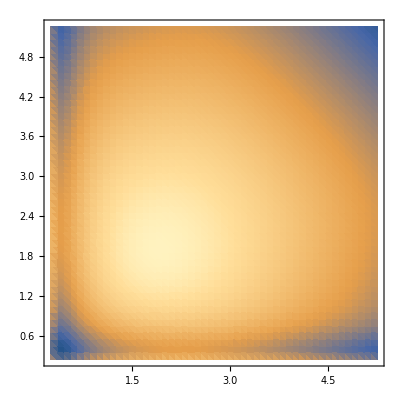

```mathematica
arrHR//QuantityMagnitude//ListDensityPlot
```

```mathematica
arrHR//QuantityMagnitude//ListPlot3D
```

-Graphics3D-

#### Basic New Dipole

```mathematica
scanLog="~/Documents/UW/Research/H5+/scans/outer_H2_scan.log";
```

```mathematica
scanData=
Developer`ToPackedArray/@
Import[scanLog, "GaussianLog", 
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
cartesianCoordinates=
Import[scanLog, "GaussianLog", 
"ImportedElements"->"CartesianCoordinates"
];
```

```mathematica
(*cartesianCoordinates=cartesianCoordinates[[1]];*)
```

```mathematica
(*Manipulate[
Graphics3D[
{Gray, PointSize[Large],
 Point[cartesianCoordinates[[i]]]},
ViewPoint->Front,
PlotRange->{{0.,8.221432},{-2.25,2.25},{0.,4.5}}
],
{i, 1, Length@cartesianCoordinates, 1}
]*)
```

```mathematica
dipCoordsOld=
Join[
scanData[["ZMatrixCoordinateVectors",All, {4, 19, 7, 16}]],
scanData[["DipoleMoments"]],
2
];
```

```mathematica
getRecenteredDipoleMoments[dCoords_]:=
Module[
{weirdRCoeff, dipVecs, qa},
qa=Developer`ToPackedArray@dCoords;
weirdRCoeff=
4.8032047128700560408`7.948154179081327
(*QuantityMagnitude[
UnitConvert["ElementaryCharge"*"BohrRadius", "Debyes"]/UnitConvert["BohrRadius", "Angstroms"]
]*);
dipVecs=
qa[[ All, {5, 6, 7}]]-
Thread[
{
weirdRCoeff*(3*qa[[All, 3]]+2*qa[[All, 4]])/5
(*(qa[[All, 3]]-qa[[All, 4]])*weirdRCoeff/2*),
0.,
weirdRCoeff*qa[[All, 1]]
}
];
Join[
Developer`ToPackedArray@qa[[All, {1, 2, 3, 4}]],
Developer`ToPackedArray@dipVecs,
2
]
];
```

```mathematica
testNewDips=
getRecenteredDipoleMoments@dipCoordsOld;
```

```mathematica
Export["~/Documents/UW/Research/H5+/inputs/recentered_dipole_surface.mx",
Interpolation[testNewDips[[All, ;;5]]]
]
```

~/Documents/UW/Research/H5+/inputs/recentered_dipole_surface.mx

#### High Res Pt 2.

```mathematica
coreDir="~/Documents/UW/Research/H5+/scans";
scanLogHR="~/Documents/UW/Research/H5+/scans/outer_H2_scan_refined.log";
scanLogHR2="~/Documents/UW/Research/H5+/scans/outer_H2_patches.log";
```

```mathematica
bleeb=
Developer`ToPackedArray/@
Import[scanLogHR, "GaussianLog", 
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
bleeb2=
Developer`ToPackedArray/@
Import[scanLogHR2, "GaussianLog", 
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
dipCoords=
Join[
Join[
bleeb[["ZMatrixCoordinateVectors",All, {4, 19, 7, 16}]],
bleeb[["DipoleMoments"]],
2
],
Join[
bleeb2[["ZMatrixCoordinateVectors",;;-2, {4, 19, 7, 16}]],
bleeb2[["DipoleMoments"]],
2
]
];
```

```mathematica
getRecenteredDipoleMoments[dCoords_]:=
Module[
{weirdRCoeff, dipVecs, qa},
qa=Developer`ToPackedArray@dCoords;
weirdRCoeff=
4.8032047128700560408`7.948154179081327
(*QuantityMagnitude[
UnitConvert["ElementaryCharge"*"BohrRadius", "Debyes"]/UnitConvert["BohrRadius", "Angstroms"]
]*);
dipVecs=
qa[[ All, {5, 6, 7}]]-
Thread[
{
weirdRCoeff*(3*qa[[All, 3]]+2*qa[[All, 4]])/5
(*(qa[[All, 3]]-qa[[All, 4]])*weirdRCoeff/2*),
0.,
weirdRCoeff*qa[[All, 1]]
}
];
Join[
Developer`ToPackedArray@qa[[All, {1, 2, 3, 4}]],
Developer`ToPackedArray@dipVecs,
2
]
];
```

```mathematica
hmm=Developer`ToPackedArray@getRecenteredDipoleMoments[dipCoords];
zerp=
AssociationThread[
hmm[[All, ;;4]],
hmm[[All, -3]]
];
```

```mathematica
noZymmNoDupes=
DeleteDuplicatesBy[
Join[
#[[{1, 2}]], 
Round[Sort@#[[{3, 4}]], .05]
]&
]@hmm[[All, ;;5]];
```

```mathematica
symmetrizedQA=
DeleteDuplicatesBy[#[[;;4]]&]@
Join[
noZymmNoDupes,
Map[
#*{1, 1,1,1, -1}&,
noZymmNoDupes[[All, {1, 2, 4, 3, 5}]]
],
Map[
#*{1, 1,1,1, -1}&,
noZymmNoDupes[[All, {2, 1, 3, 4, 5}]]
],
Map[
#*{1, 1,1,1, -1}&,
noZymmNoDupes[[All, {2, 1, 4, 3, 5}]]
]
];
```

```mathematica
notStupidCoordinates=
Select[symmetrizedQA, #[[1]]<1.2&&#[[2]]<1.2&];
```

```mathematica
gg=GroupBy[notStupidCoordinates, #[[;;2]]&->(#[[{3, 4}]]&)];
```

```mathematica
fullKeys=Keys@Select[Length/@gg, #>90&];
```

```mathematica
wtf=Interpolation[ notStupidCoordinates[[All, ;;5]] ];
```

Interpolation::indim: The coordinates do not lie on a structured tensor product grid.

```mathematica
dipoleQA=
QuantityArray[
viablePoints,
{"Angstroms", "Angstroms", "Angstroms", "Angstroms", "Debyes", "Debyes", "Debyes"}
]
```

```mathematica
Export["~/Documents/UW/Research/H5+/inputs/h5_dip_QA_3.mx", dipoleQA]
```

~/Documents/UW/Research/H5+/inputs/h5_dip_QA_3.mx

```mathematica
.0717
```

#### Expansion 1

```mathematica
coreDir="~/Documents/UW/Research/H5+/scans";
expansion="~/Documents/UW/Research/H5+/scans/outer_H2_scan_expanded_1.log";
```

```mathematica
expShit=
Developer`ToPackedArray/@
Import[expansion, "GaussianLog", 
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
impShit=Import["~/Documents/UW/Research/H5+/inputs/h5_4D_H_center_scan_pot_QA.mx"];
```

```mathematica
expFuckerRaw=
Join[
expShit[["ZMatrixCoordinateVectors",
;;Length@expShit[["MP2Energies"]], 
{4, 19, 7, 16}
]],
Transpose@List[
QuantityMagnitude[ChemUnitConvert["Hartrees", "Wavenumbers"]]*expShit[["MP2Energies"]]
],
2
];
expFucker=
QuantityArray[
Pick[expFuckerRaw, UnitStep[4.5-expFuckerRaw[[All, 3]]], 1],
impShit[[1]]//QuantityUnit
];
```

```mathematica
fuckThisFull=
QuantityArray[
Select[
Sort@
DeleteDuplicatesBy[
Join[
QuantityMagnitude@impShit, 
QuantityMagnitude@expFucker,
QuantityMagnitude@expFucker[[All, {2, 1, 4,3, 5}]]
],
#[[;;4]]&
],
#[[1]]<2.35&&#[[2]]<2.35&
],
QuantityUnit[impShit[[1]]]
];
```

```mathematica
(*Export[
"~/Documents/UW/Research/H5+/inputs/h5_4D_H_center_scan_pot_QA_2.mx",
fuckThisFull
]*)
```

~/Documents/UW/Research/H5+/inputs/h5_4D_H_center_scan_pot_QA_2.mx

```mathematica
expFuckerDipRaw=
Join[
expShit[["ZMatrixCoordinateVectors",
;;Length@expShit[["DipoleMoments"]], 
{4, 19, 7, 16}
]],
expShit[["DipoleMoments"]],
2
];
```

```mathematica
expFuckerDip=
QuantityArray[
Pick[expFuckerDipRaw, UnitStep[4.5-expFuckerDipRaw[[All, 3]]], 1],
Join[QuantityUnit[impShit[[1]]][[;;4]], ConstantArray["Debyes", 3]]
];
```

```mathematica
getRecenteredDipoleMoments[dCoords_]:=
Module[
{weirdRCoeff, dipVecs, qa},
qa=Developer`ToPackedArray@dCoords;
weirdRCoeff=
4.8032047128700560408`7.948154179081327
(*QuantityMagnitude[
UnitConvert["ElementaryCharge"*"BohrRadius", "Debyes"]/UnitConvert["BohrRadius", "Angstroms"]
]*);
dipVecs=
qa[[ All, {5, 6, 7}]]-
Thread[
{
weirdRCoeff*(3*qa[[All, 3]]+2*qa[[All, 4]])/5
(*(qa[[All, 3]]-qa[[All, 4]])*weirdRCoeff/2*),
0.,
weirdRCoeff*qa[[All, 1]]
}
];
Join[
Developer`ToPackedArray@qa[[All, {1, 2, 3, 4}]],
Developer`ToPackedArray@dipVecs,
2
]
];
```

```mathematica
recenteredDipFucker=
QuantityArray[
getRecenteredDipoleMoments@QuantityMagnitude@expFuckerDip,
QuantityUnit[expFuckerDip]
];
```

```mathematica
oldFuckerRaw=
Import[
"/Users/Mark/Documents/UW/Research/H5+/scans/outer_H2_scan.log",
"GaussianLog",
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
oldFucker=
Join[
oldFuckerRaw[["ZMatrixCoordinateVectors",
;;Length@oldFuckerRaw[["DipoleMoments"]], 
{4, 19, 7, 16}
]],
oldFuckerRaw[["DipoleMoments"]],
2
];
```

```mathematica
expFuckerDip2=
QuantityArray[
Round[#, .0000001]&@
Select[
Sort@
DeleteDuplicatesBy[
Developer`ToPackedArray@N@Join[ 
QuantityMagnitude@oldFucker(*Map[
#+{.000031, .000031, .000016, .000016, 0, 0, 0}&,
QuantityMagnitude@oldFucker
]*),
Map[#*{1, 1,1, 1, -1, 1, 1}&,QuantityMagnitude@oldFucker[[All, {2, 1, 4,3, 5, 6, 7}]]
],
QuantityMagnitude@recenteredDipFucker,
Map[#*{1, 1,1, 1, -1, 1, 1}&,QuantityMagnitude@recenteredDipFucker[[All, {2, 1, 4,3, 5, 6, 7}]]
]
],
#[[;;4]]&
],
#[[1]]<2.35&&#[[2]]<2.35&
],
QuantityUnit[oldFucker[[1]]]
];
```

```mathematica
expFuckerDip2[[All, ;;5]]//Interpolation
```

```mathematica
shitFuck=GroupBy[QuantityMagnitude@expFuckerDip2, (#[[;;2]]&)->(#[[{3, 4}]]&)];
```

```mathematica
shitFuck[[1]]//Transpose//Map[Differences@*Sort@*DeleteDuplicates]
```

{{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2},{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2}}

```mathematica
Keys[shitFuck]
```

```mathematica
Keys[shitFuck]//Transpose//Map[Differences@*Sort@*DeleteDuplicates]
```

```mathematica
shitFuck[[1]]//Transpose//Map[Differences@*Sort@*DeleteDuplicates]
```

```mathematica
0.510716+.17*Range[22]
```

{0.680716,0.850716,1.02072,1.19072,1.36072,1.53072,1.70072,1.87072,2.04072,2.21072,2.38072,2.55072,2.72072,2.89072,3.06072,3.23072,3.40072,3.57072,3.74072,3.91072,4.08072,4.25072}

```mathematica
{{0.510716,0.680716,0.710716,0.8507159999999999,0.910716,1.020716,1.110716,1.1907159999999999,1.310716,1.360716,1.510716,1.530716,1.700716,1.710716,1.8707159999999998,1.9107159999999999,2.0407159999999998,2.110716,2.2107159999999997,2.3107159999999998,2.380716,2.510716,2.550716,2.7107159999999997,2.720716,2.890716,2.910716,3.0607159999999998,3.110716,3.2307159999999997,3.3107159999999998,3.4007159999999996,3.510716,3.570716,3.7107159999999997,3.740716,3.910716,4.080716,4.250716},{0.510716,0.680716,0.710716,0.8507159999999999,0.910716,1.020716,1.110716,1.1907159999999999,1.310716,1.360716,1.510716,1.530716,1.700716,1.710716,1.8707159999999998,1.9107159999999999,2.0407159999999998,2.110716,2.2107159999999997,2.3107159999999998,2.380716,2.510716,2.550716,2.7107159999999997,2.720716,2.890716,2.910716,3.0607159999999998,3.110716,3.2307159999999997,3.3107159999999998,3.4007159999999996,3.510716,3.570716,3.7107159999999997,3.740716,3.910716,4.080716,4.250716}}
```

```mathematica
Length/@shitFuck//DeleteDuplicates
```

<|{0.255831,0.255831}→418|>

```mathematica
shitFuck
```

```mathematica
Select[expFuckerDip2]
```

Select[StructuredArray[QuantityArray, {56600, 7}, <{Angstroms, Angstroms, Angstroms, Angstroms, Debyes, Debyes, Debyes}>]]

```mathematica
fuckThisFull
```

StructuredArray[QuantityArray, {52900, 5}, <{Angstroms, Angstroms, Angstroms, Angstroms, Wavenumbers}>]

## Refined WTF?

```mathematica
expShit2=
Developer`ToPackedArray/@
Import["/Users/Mark/Desktop/outer_H2_scan_refined.log", "GaussianLog", 
"ImportedElements"->
{
"ZMatrixCoordinateVectors",
"MP2Energies",
"DipoleMoments"
}
];
```

```mathematica
expShit2["ZMatrixCoordinateVectors"]//Length
```

14556